```mathematica
Входные данные;
```

```mathematica
ϵ=0.001;X0={-√5,0};α=200;
f[{x_,y_}]:=8 x^2+5 y^2-4x y +8 √5 (x+2y)+64;(*α(x^2-y)^2+(x-1)^2*)
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],{x,y}]/.{x->x1,y->x2}
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]]
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
HesseF[{x1_,y1_}] :=( Grad[Grad[f[{x,y}],{x,y}],{x,y}])/.{x->x1,y->y1};
X=X0;
points={X0};
norm={NormGradF[X0]};
fValues={f[X0]};
pArray={};
μ =0.5;
Clear[κ]
```

```mathematica
Метод Ньютона;
```

Результат получен за 1 итер.: X = {-2.23607, -4.47214}

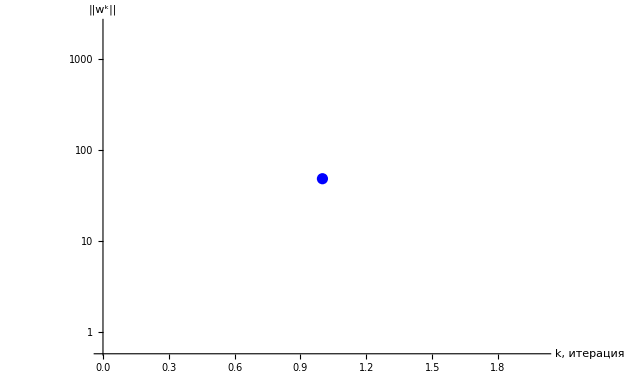

```mathematica
While[norm[[-1]]≥ ϵ,
w=antiGradF[X];
hessePositive = HesseF[X];
While[!PositiveDefiniteMatrixQ[hessePositive ],hessePositive +=μ IdentityMatrix[2]];

p=Inverse[HesseF[X]]. w//N;
X+= p;
fValues=Append[fValues,f[X]];
norm=Append[norm,NormGradF[X]];
points=Append[points,X];
];



(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"}]
```

Part::take: Cannot take positions 1 through 4 in {64,-36.}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partw: Part 3 of {64,-36.} does not exist.

Part::partw: Part 6 of {64,-36.} does not exist.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 4 in {64,-36.}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Part::partw: Part 3 of {64,-36.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Contours::ilevels: Join[{64.,51.2002,38.4005,25.6007,12.801,0.00124225,-12.7985,-25.5983,-38.398,-51.1978,-63.9975,-36.,22.,80.},{64,-36.}⟦1;;4⟧,{{64,-36.}⟦3⟧,{64,-36.}⟦6⟧}] is not a valid mesh specification.

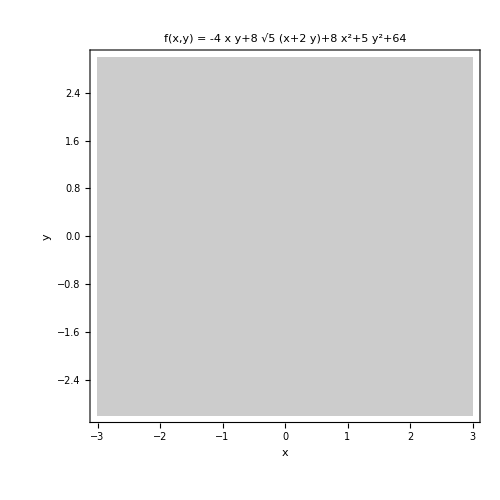

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[3]],fValues[[6]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500]
```

Part::take: Cannot take positions 1 through 4 in {64,-36.}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partw: Part 3 of {64,-36.} does not exist.

Part::partw: Part 6 of {64,-36.} does not exist.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 4 in {64,-36.}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Part::partw: Part 3 of {64,-36.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Contours::ilevels: Join[{64.,51.2002,38.4005,25.6007,12.801,0.00124225,-12.7985,-25.5983,-38.398,-51.1978,-63.9975,-36.,22.,80.},{64,-36.}⟦1;;4⟧,{{64,-36.}⟦3⟧,{64,-36.}⟦6⟧}] is not a valid mesh specification.

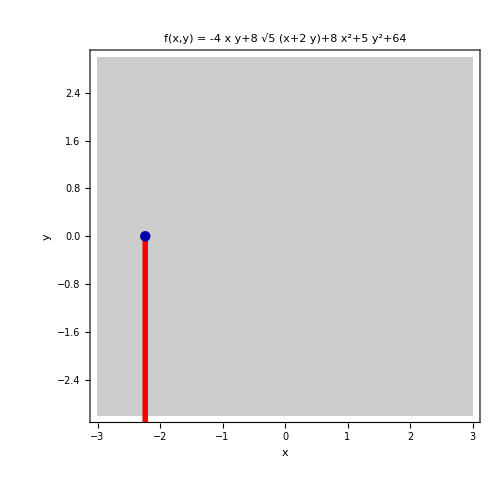

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[3]],fValues[[6]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[norm];
gridLabel={"k","X^k","f(X^k)","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;6]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

Part::take: Cannot take positions 1 through 6 in {{k,X^k,f(X^k),||w^k||},{0,( -2.2360680,      -8
0. 10 ),64.0000000,48.166378},{1,( -2.2360680, -4.4721360 ),-36.0000000,0.}}.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Grid[Join[{{k,X^k,f(X^k),||w^k||},{0,( -2.2360680,      -8
0. 10 ),64.0000000,48.166378},{1,( -2.2360680, -4.4721360 ),-36.0000000,0.}}⟦1;;6⟧,{{...,...,...,...}},{{0,( -2.2360680,      -8
0. 10 ),64.0000000,48.166378},{1,( -2.2360680, -4.4721360 ),-36.0000000,0.}}],Dividers→{{1→True,2→True,3→True,4→True,5→True},True},FrameStyle→Thickness[Large],Spacings→{2,2},ItemStyle→Directive[FontSize→15],Background→{None,{{RGBColor[0.9, 1, 1],RGBColor[0.87, 0.94, 1]}}}]

```mathematica
X
```

{-2.23607,-4.47214}

```mathematica
Модификация метода Ньютона с дроблением шага;
```

Результат получен за 21 итер.: X = {-2.23607, -4.47217}

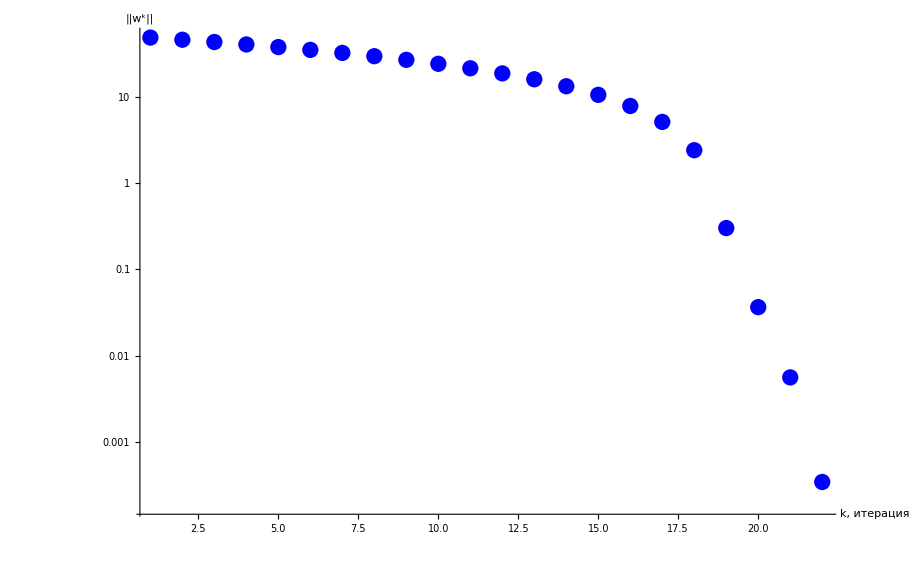

```mathematica
Clear[κ];
κ=0.5;
κArray={κ};
X=X0;
points={X0};
norm={NormGradF[X0]};
fValues={f[X0]};
pArray={};
μ =0.5;
ω=0.4;

While[norm[[-1]]≥ ϵ,
w=antiGradF[X];
hessePositive = HesseF[X];
While[!PositiveDefiniteMatrixQ[hessePositive ],hessePositive +=μ IdentityMatrix[2]];
p=Inverse[HesseF[X]]. w//N;
p=p/Norm[p];
Xpos=X+κ antiGradF[X];
While[f[X]-f[Xpos]< ω κ (w.p) ,
κ=κ/2;
Xpos=X+κ p;

];
κArray=Append[κArray,κ];κ=0.5;

X=Xpos;
points=Append[points,X];
fValues=Append[fValues,f[X]];
norm=Append[norm,NormGradF[X]];
];
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"}]
```

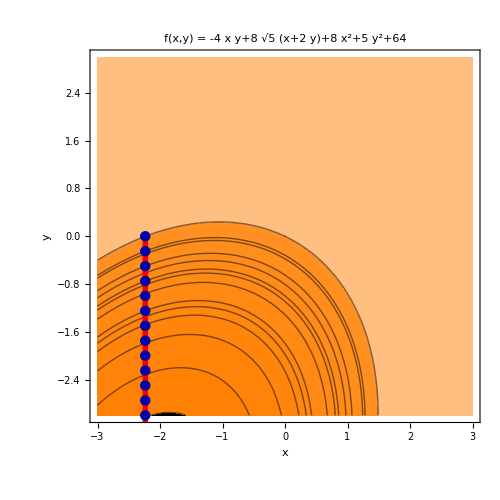

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[3]],fValues[[6]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[norm];
gridLabel={"k","X^k","f(X^k)","κ_k","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[κArray,8];
gridData[[All,5]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;6]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | κ_k | ||w^k||
0 | ( -2.2360680,      -8
0. 10 ) | 64.0000000 | 0.5 | 48.166378
1 | ( -2.2360680, -0.2500000 ) | 53.1321601 | 0.25 | 45.4737959
2 | ( -2.2360680, -0.5000000 ) | 42.8893202 | 0.25 | 42.7812135
3 | ( -2.2360680, -0.7500000 ) | 33.2714803 | 0.25 | 40.0886311
4 | ( -2.2360680, -1.0000000 ) | 24.2786405 | 0.25 | 37.3960487
... | ... | ... | ... | ...
16 | ( -2.2360680, -4.0000000 ) | -34.8854382 | 0.25 | 5.0850599
17 | ( -2.2360680, -4.2500000 ) | -35.7532781 | 0.25 | 2.3924775
18 | ( -2.2360680, -4.5000000 ) | -35.9961180 | 0.25 | 0.3001049
19 | ( -2.2360680, -4.4687500 ) | -35.9999427 | 0.03125 | 0.0364679
20 | ( -2.2360680, -4.4726562 ) | -35.9999986 | 0.0039063 | 0.0056037
21 | ( -2.2360680, -4.4721680 ) | -36.0000000 | 0.0004883 | 0.0003448

```mathematica
Модификация метода Ньютона с наискорейшим спуском;
```

Результат получен за 1 итер.: X = {-2.23607, -4.47214}

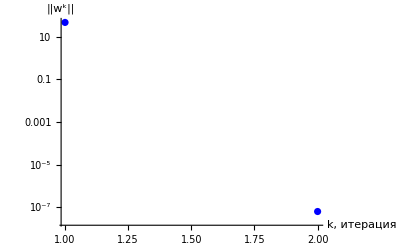

```mathematica
Clear[κ];
κ=0.5;
κArray={κ};
X=X0;
points={X0};
norm={NormGradF[X0]};
fValues={f[X0]};
pArray={};
μ =0.5;
ω=0.4;

While[norm[[-1]]≥ ϵ,
w=antiGradF[X];
hessePositive = HesseF[X];
While[!PositiveDefiniteMatrixQ[hessePositive ],hessePositive +=μ IdentityMatrix[2]];
p=Inverse[HesseF[X]]. w//N;
p=p/Norm[p];
κ = NArgMin[f[X+ka p],ka];
Xpos=X+κ p;

κArray=Append[κArray,κ];κ=0.5;
X=Xpos;
points=Append[points,X];
fValues=Append[fValues,f[X]];
norm=Append[norm,NormGradF[X]];
];
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"}]
```

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[3]],fValues[[6]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

Part::take: Cannot take positions 1 through 4 in {64,-36.}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partw: Part 3 of {64,-36.} does not exist.

Part::partw: Part 6 of {64,-36.} does not exist.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 4 in {64,-36.}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Part::partw: Part 3 of {64,-36.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Contours::ilevels: Join[{64.,51.2002,38.4005,25.6007,12.801,0.00124225,-12.7985,-25.5983,-38.398,-51.1978,-63.9975,-36.,22.,80.},{64,-36.}⟦1;;4⟧,{{64,-36.}⟦3⟧,{64,-36.}⟦6⟧}] is not a valid mesh specification.

-Graphics-

```mathematica
len=Length[norm];
gridLabel={"k","X^k","f(X^k)","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;6]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

Part::take: Cannot take positions 1 through 6 in {{k,X^k,f(X^k),||w^k||},{0,( -2.2360680,      -8
0. 10 ),64.0000000,48.166378},{1,( -2.2360680, -4.4721360 ),-36.0000000,6.×10^-8}}.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Grid[Join[{{k,X^k,f(X^k),||w^k||},{0,( -2.2360680,      -8
0. 10 ),64.0000000,48.166378},{1,( -2.2360680, -4.4721360 ),-36.0000000,6.×10^-8}}⟦1;;6⟧,{{...,...,...,...}},{{0,( -2.2360680,      -8
0. 10 ),64.0000000,48.166378},{1,( -2.2360680, -4.4721360 ),-36.0000000,6.×10^-8}}],Dividers→{{1→True,2→True,3→True,4→True,5→True},True},FrameStyle→Thickness[Large],Spacings→{2,2},ItemStyle→Directive[FontSize→15],Background→{None,{{RGBColor[0.9, 1, 1],RGBColor[0.87, 0.94, 1]}}}]